## Hexi—PS10—2025-02-25

### Exercises from EIWL3 Section 26

```mathematica
#^2&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Blend[{#,Red}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
Framed[Column[{ToUpperCase[#],ToLowerCase[#]}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






France | Germany | Japan | United Kingdom | United States
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Framed[Grid[{#["Name"],#["Flag"]}]]&@EntityClass["Country","GroupOf5"]
```

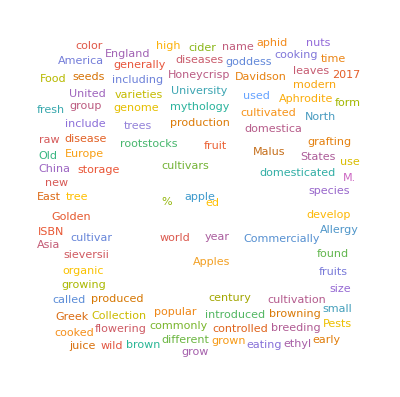
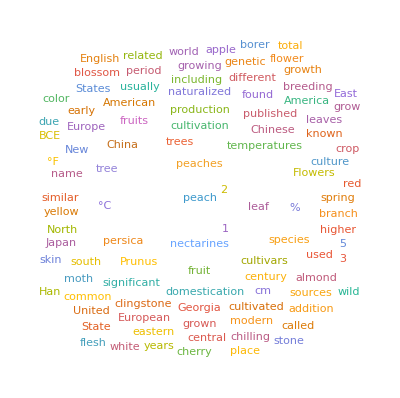
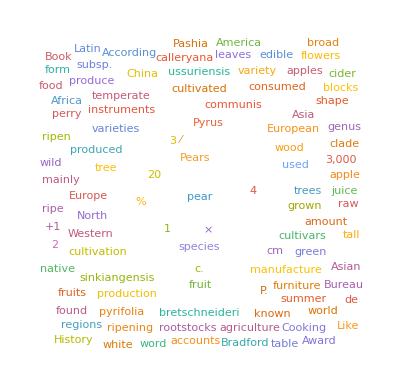

```mathematica
WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

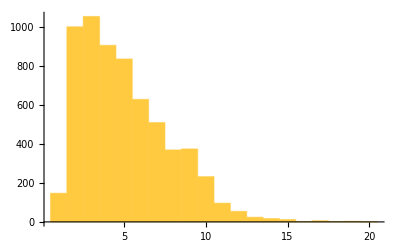
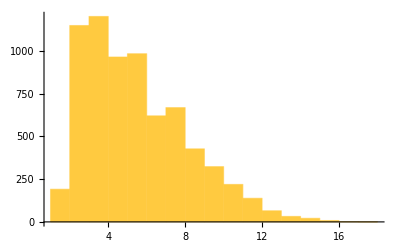
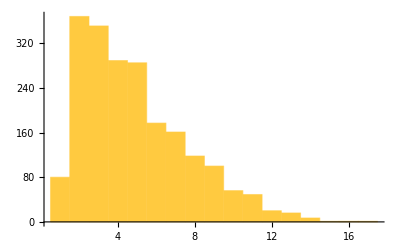

```mathematica
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

```mathematica
GeoGraphics[{GeoStyling[Red],Polygon[#]},GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Exercises from EIWL3 Section 27

```mathematica
NestList[Blur[#]&,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Framed[Rotate[#,RandomInteger[360]°]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

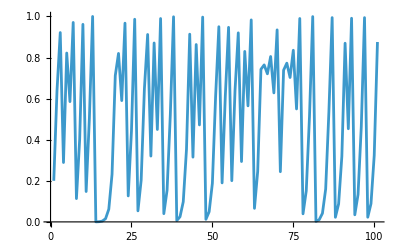

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

```mathematica
Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
NestList[3 #&,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

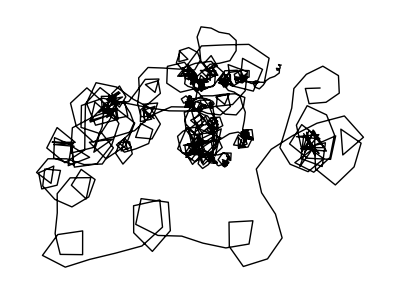

```mathematica
Graphics[Line[AnglePath[NestList[#+{RandomReal[{-1,1}],RandomReal[{-1,1}]}&,{0,0},1000]]]]
```

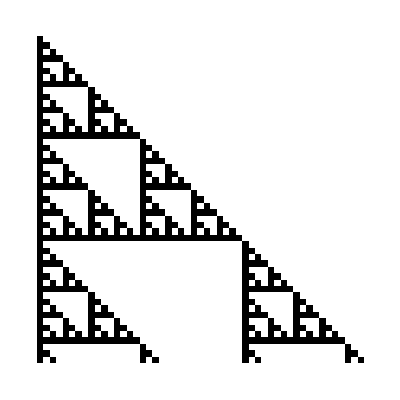

```mathematica
NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]//ArrayPlot
```

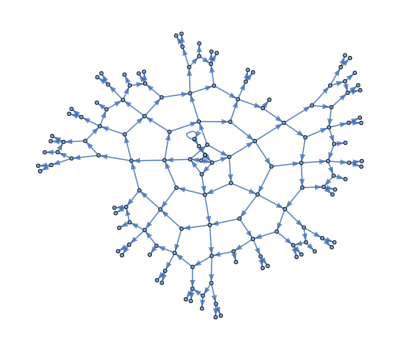

```mathematica
NestGraph[{2#,#+1}&,0,10]
```

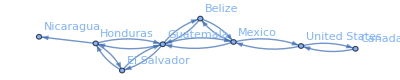

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->Automatic]
```

### Exercises from EIWL3 Section 27

```mathematica
123^321>456^123
```

True

```mathematica
Select[Range[100],Total[IntegerDigits[#]]<5&]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Select[WordList[],StringMatchQ[#,"p"~~__~~"p"]&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
Select[Prime[Range[100]],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[Range[100]],!StringContainsQ[#,"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral/@Range[1000],#==StringReverse[#]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[IntegerName/@Range[100],First@Characters[#]==Last@Characters[#]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

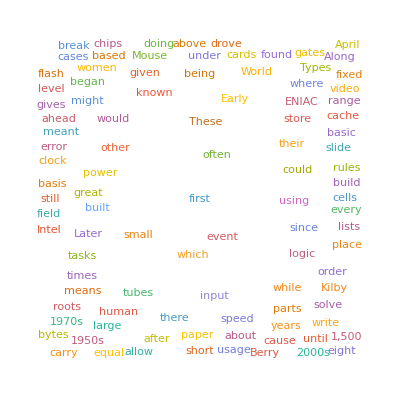

```mathematica
WordCloud[Select[TextWords@WikipediaData["computer"],StringLength[#]==5&]]
```

```mathematica
Select[WordList[],StringTake[#,3]==StringReverse[StringTake[#,-3]]&&#!=StringReverse[#]&]
```

StringTake::take: Cannot take positions 1 through 3 in "a".

StringTake::take: Cannot take positions -3 through -1 in "a".

StringReverse::string: String expected at position 1 in StringReverse[StringTake[a,-3]].

StringTake::take: Cannot take positions 1 through 3 in "ad".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

StringReverse::string: String expected at position 1 in StringReverse[StringTake[ad,-3]].

StringReverse::string: String expected at position 1 in StringReverse[StringTake[ah,-3]].

General::stop: Further output of StringReverse::string will be suppressed during this calculation.

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[WordList[],StringLength[#]==10&&Total@LetterNumber@Characters[#]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}